```mathematica
domainSize=128;
fftDx=(2Pi/domainSize)Table[I x,{x,0,domainSize-1},{y,0,domainSize-1}];
fftDy=(2Pi/domainSize)Table[I y,{x,0,domainSize-1},{y,0,domainSize-1}];
fftD2=fftDx^2+fftDy^2;
fftID2=Map[If[#==0,0,1/#]&,fftD2,{2}];
(* Perform the operation f via multiplication in the Fourier domain *)
viaFFT[f_,ex_]:=(*Transpose@*)Re@InverseFourier[f Fourier[ex]];
curlDiscrete[ex_]:=viaFFT[fftDx,ex[[All,All,2]]]-viaFFT[fftDy,ex[[All,All,1]]]
uncurlDiscrete[ex_]:={viaFFT[fftDy,ex],viaFFT[-fftDx,ex]}
gradDiscrete[ex_]:={viaFFT[fftDx,ex],viaFFT[fftDy,ex]}
toVectorFieldRepr[ex_]:=Transpose[ex,{2,3,1}]
streamFuncDiscrete[ex_]:=viaFFT[-fftID2,curlDiscrete[ex]]
(*
discreteHess[ex_,pt_]:={{ListInterpolation[viaFFT[fftDx^2,ex]]@@pt,ListInterpolation[viaFFT[fftDx fftDy,ex]]@@pt},{ListInterpolation[viaFFT[fftDx fftDy,ex]]@@pt,ListInterpolation[viaFFT[fftDy^2,ex]]@@pt}}
*)
discreteHess[ex_,pt_]:={{Extract[viaFFT[fftDx^2,ex],pt],Extract[viaFFT[fftDx fftDy,ex],pt]},{Extract[viaFFT[fftDx fftDy,ex],pt],Extract[viaFFT[fftDy^2,ex],pt]}}
vortToVelocity[vort_]:=gradDiscrete[streamFuncDiscrete[vort]]
Clear[discreteToInterp,discreteToInterpNoMod,interpToDiscrete]
discreteToInterp[dis_]:=discreteToInterp[dis]=ListInterpolation[dis,{{0,2Pi},{0,2Pi}}][Mod[x,2Pi],Mod[y,2Pi]];
discreteToInterpNoMod[dis_]:=discreteToInterpNoMod[dis]=ListInterpolation[dis,{{0,2Pi},{0,2Pi}}];
interpToDiscrete[ifun_]:=interpToDiscrete[ifun]=Table[ifun[x(2Pi/domainSize),y(2Pi/domainSize)],{x,0,domainSize-1},{y,0,domainSize-1}];
skewDiscrete[l_]:=Map[{-#[[2]],#[[1]]}&,l,{2}];
```

```mathematica
(1+dt/4 L)/(1/(1-dt/4 L))/.{L->nu d2-alpha}//Simplify
```

-1/16 (-4+alpha dt-d2 dt nu) (4+alpha dt-d2 dt nu)

```mathematica
-beta*(u_tmp.*omx_tmp+v_tmp.*omy_tmp)
-β(u viaFFT[fftDx,ω+dt/2 k1]+v viaFFT[fftDy,ω+dt/2 k1])
```

```mathematica
dtSize=30/3840//N
Clear[dt]
```

0.0078125

```mathematica
Fourier
```

```mathematica
getDerivativeOmega[omega_]:=uncurlDiscrete[viaFFT[-fftID2,omega]]gradDiscrete[omega]//Total
```

```mathematica
dom=Cuboid[{0,0},{2Pi,2Pi}];
dsol=NDSolveValue[{D[ω[x,y,t],t]==getDerivativeOmega[interpToDiscrete[ω[#1,#2,t]&]],ω[x,y,0]==discreteToInterpNoMod[omegaZero][x,y]},ω[x,y,t],{t,0,1},{x,0,2Pi},{y,0,2Pi}]
```

Fourier::fftl: Argument {{ω[0,0,t],ω[0,π/64,t],ω[0,π/32,t],ω[0,(3 π)/64,t],ω[0,π/16,t],ω[0,(5 π)/64,t],ω[0,(3 π)/32,t],ω[0,(7 π)/64,t],ω[0,π/8,t],ω[0,(9 π)/64,t],«118»},{ω[π/64,0,t],ω[π/64,π/64,t],ω[π/64,π/32,t],ω[π/64,(3 π)/64,t],ω[π/64,π/16,t],ω[π/64,(5 π)/64,t],ω[π/64,(3 π)/32,t],ω[π/64,(7 π)/64,t],ω[π/64,π/8,t],ω[π/64,(9 π)/64,t],«118»},«8»,«118»} is not a non-empty list or rectangular array of numeric quantities.

InverseFourier::fftl: Argument {<<78735789056 bytes>>} is not a non-empty list or rectangular array of numeric quantities.

$Aborted

```mathematica
Plot3D[dsol/.t->1,{x,0,2Pi},{y,0,2Pi}]
```

-Graphics3D-

```mathematica
fftD2//TensorDimensions
fftID2//TensorDimensions
```

{128,128}

{128,128}

```mathematica
dtSize getDerivativeOmega[omegaZero]//Flatten//StandardDeviation
severalPsiExamples[[2]]-severalPsiExamples[[1]]//Flatten//StandardDeviation
```

148446.

0.0869457

```mathematica
omegaZero=viaFFT[fftD2,severalPsiExamples[[1]]];
ListPlot3D@omegaZero
getDerivativeOmega[omegaZero]//ListPlot3D
severalPsiExamples[[2]]-severalPsiExamples[[1]]//ListPlot3D
```

ListPlot3D::arrayerr: getDerivativeOmega[{{-1082.84,-1112.74,-1138.89,-1161.26,-1179.83,-1194.6,-1205.58,-1212.8,-1216.27,-1216.06,«118»},«9»,«118»}] must be a valid array or a list of valid arrays.

```mathematica
discreteToInterp[severalPsiExamples[[1]]]
```

```mathematica
[Mod[x,2 π],Mod[y,2 π
```

## Charge detection stuff

```mathematica
mkElp[hessEigs_,pt_]:=ParametricPlot[10Sqrt[hessEigs[[1]][[1]]hessEigs[[1]][[2]]](Cos[t]/hessEigs[[1]][[1]]hessEigs[[2]][[1]]+Sin[t]/hessEigs[[1]][[2]]hessEigs[[2]][[2]])+pt,{t,0,2Pi},PlotStyle->{Thick,Green}];
mkEigenGraphics[xs_,pt_]:=Module[{hessEigs,elp,magn,point},
hessEigs=Eigensystem@discreteHess[xs,pt](*//EchoLabel["eigs"]*);
elp=mkElp[hessEigs,pt];
magn=Graphics[Text[StringForm["γ = ``",Log@Det@discreteHess[xs,pt]],pt+{0,5}]];
point=Graphics[Point[pt]];
{elp,magn,point}
]
```

```mathematica
drawDiagram[xs_]:=Module[{cp,maxCoord,maxPt,minCoord,minPt,elpMax,elpMin,magnMax,magnMin,hessEigsMax,hessEigsMin},
cp=ListContourPlot[Transpose[xs],PerformanceGoal->"Quality",PlotLabel->"Stream function contour plot, rest frame of minimum",PlotRangePadding->Scaled[.1],ImageSize->Large];
maxCoord=Position[xs,Max[xs]][[1]];
minCoord=Position[xs,Min[xs]][[1]];
Image[Show[{cp,mkEigenGraphics[xs,maxCoord],mkEigenGraphics[xs,minCoord]}]]
]
getReducedData[xs_]:=Module[{maxCoord,xxStr,yyStr},
maxCoord=Position[xs,Max[xs]][[1]];
xxStr=-Extract[discreteDxx[xs],maxCoord];
yyStr=-Extract[discreteDyy[xs],maxCoord];
{maxCoord,xxStr,yyStr}
]
```

```mathematica
ListContourPlot[Transpose@scatteredPsi[[12]],Contours->50]
```

-Graphics-

```mathematica
drawDiagram[scatteredPsi[[12]]]
```

-Graphics-

```mathematica
(*allPsi=Uncompress@Import["allPsi.txt"]
Clear[frames]*)
```

```mathematica
frames=ParallelMap[Image[drawDiagram@#]&,(allPsi[[;;;;5]])];
Export["rotatedDiagramsLong.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"->0.1]
```

rotatedDiagramsLong.gif

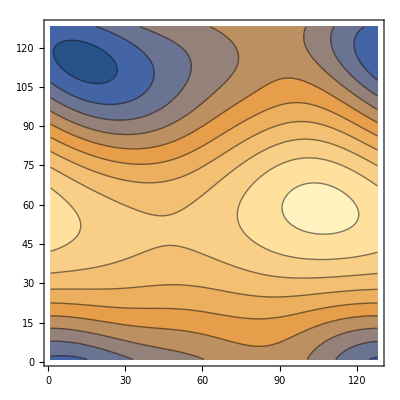

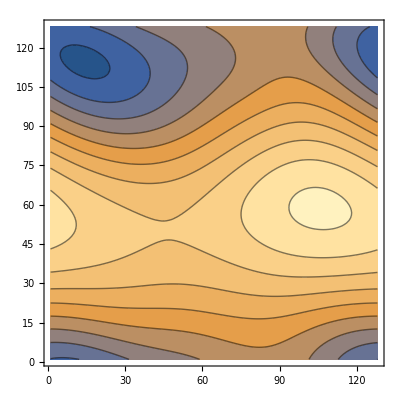

```mathematica
ListContourPlot[Transpose@scatteredPsi[[30]]]
ListContourPlot[-Transpose@viaFFT[fftDy^2 + fftDx^2- fftDx fftDy,scatteredPsi[[30]]]]
(*hessFunc=Evaluate@(D[discreteToInterpNoMod[scatteredPsi[[30]]][x,y],{x,2}]D[discreteToInterpNoMod[scatteredPsi[[30]]][x,y],{y,2}]-D[D[discreteToInterpNoMod[scatteredPsi[[30]]][x,y],x],y]^2)
ContourPlot[hessFunc,{x,0,2Pi},{y,0,2Pi}]*)
```

```mathematica
InverseFourier[fftDy^2 + fftDx^2- fftDx fftDy]//Im//ListPlot3D
```

-Graphics3D-

```mathematica
failureOfEqualsDetDel[xs_]:=Standardize[Flatten[-viaFFT[fftDy^2 + fftDx^2 - fftDx fftDy,xs]]]-Standardize[Flatten[xs]]//Abs//Total;
fails=failureOfEqualsDetDel/@scatteredPsi
```

{15.3864,14.7589,12.1457,14.0276,12.1914,4.83795,9.52079,12.8354,13.8875,17.202,23.8056,23.1145,26.0414,22.2636,13.4181,7.02754,11.3666,10.2906,6.91853,7.64522,10.415,17.5745,17.8521,18.3676,12.656,8.55015,14.1638,16.6681,11.6427,13.288,9.66418,5.08646,6.01912,9.61598,8.1076,4.83383,6.83955,11.7854,12.3307,12.1616,15.4421,20.2548,25.296,30.2881,29.4909,27.3365,23.2729,19.0436,21.1613,20.7273,18.5141,15.003,11.5856,4.26425}

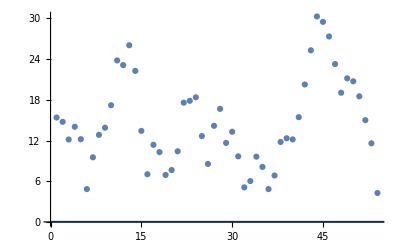

```mathematica
Show[ListPlot@fails,Plot[$MachineEpsilon,{x,0,60}]]
```

```mathematica
getShift[xs_]:=Flatten[-viaFFT[fftDy^2 + fftDx^2 - fftDx fftDy,xs]]/Flatten[xs]//Mean
```

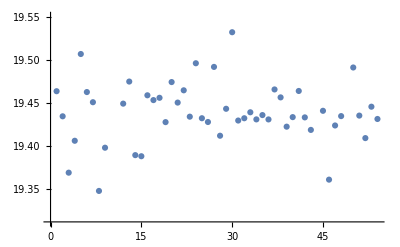

```mathematica
ListPlot[getShift/@scatteredPsi]
```

```mathematica
scatteredDetDels=viaFFT[fftDy^2 + fftDx^2 - fftDx fftDy,#]&/@scatteredPsi;
```

```mathematica
viaFFT[fftDy^2 + fftDx^2 - fftDx fftDy,scatteredPsi[[30]]]/scatteredPsi[[30]]//ListPlot3D
```

-Graphics3D-

```mathematica
NDEigensystem[{D[ux[x,y],x]D[uy[x,y],y]-D[ux[x,y],y]D[uy[x,y],x],D[ux[x,y],y]-D[uy[x,y],x]},{ux[x,y],uy[x,y]},{x,0,2Pi},{y,0,2Pi},3]
```

NDEigensystem::stlin: Coefficients and boundary conditions need to be stationary and linear.

NDEigensystem[{uy^(0,1)[x,y] ux^(1,0)[x,y]-ux^(0,1)[x,y] uy^(1,0)[x,y],ux^(0,1)[x,y]-uy^(1,0)[x,y]},{ux[x,y],uy[x,y]},{x,0,2 π},{y,0,2 π},3]

```mathematica
failureOfEqualsDetDel[interpToDiscrete[func]]
```

-3.64153×10^-14

Cos[#1] Sin[3 #2]&

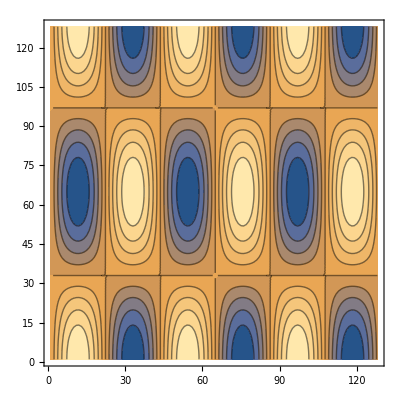

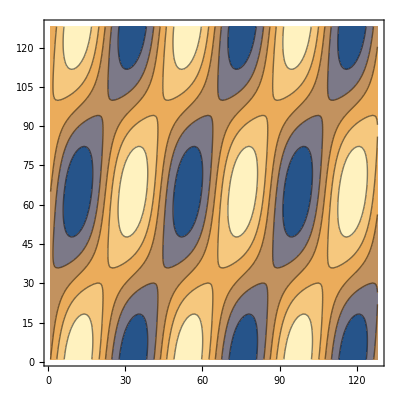

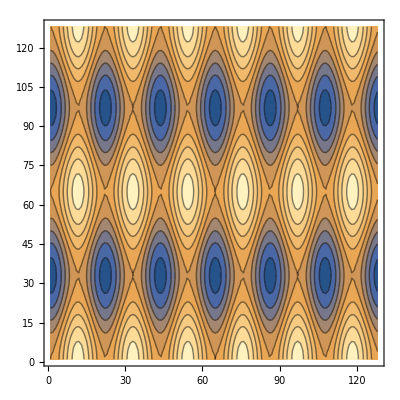

```mathematica
func=Cos[#1]Sin[3 #2]&
interpToDiscrete[func]//ListContourPlot
-viaFFT[fftDy^2 + fftDx^2 - fftDx fftDy,interpToDiscrete[func]]//ListContourPlot
interpToDiscrete[9(Cos[#1]^2Sin[3#2]^2-Sin[#1]^2Cos[3#2]^2)&]//ListContourPlot
```

```mathematica
20interpToDiscrete[func]+viaFFT[fftDy^2 + fftDx^2 - fftDx fftDy,interpToDiscrete[func]]//ListContourPlot
```

-Graphics-

```mathematica
ListPointPlot3D[severalPsiExamples[[10]]]
ListPointPlot3D[Fourier[severalPsiExamples[[1]]][[;;8,;;8]]//Abs,PlotRange->All,PlotStyle->OpacityFunction]
ListPointPlot3D[Fourier[severalPsiExamples[[1]]][[;;8,;;8]]//Arg,PlotRange->All,PlotStyle->OpacityFunction]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
bottom4[xs_]:=Fourier[xs][[;;4,;;4]];
ListPointPlot3D[bottom4@severalPsiExamples[[10]]-bottom4@severalPsiExamples[[1]]//Abs,PlotRange->All]
```

-Graphics3D-

```mathematica
l=16
fullZeros=Table[0,{x,l},{y,l}];
Manipulate[
ListContourPlot[ReplacePart[fullZeros,{{1,1}->500,{1,2}->a 100 Exp[I t],{2,1}->b 100 Exp[I p],{1,l}->a 100 Exp[-I t],{l,1}->b 100 Exp[-I p],{l,l}->c 100 Exp[-I r],{2,2}->c 100 Exp[I r]}]//InverseFourier,PerformanceGoal->"Quality"]
,{a,1,10},{b,1,10},{c,1,10},{t,0,2Pi},{p,0,2Pi},{r,0,2Pi}]
```

16

ReplacePart::pkspec1: The expression l cannot be used as a part specification.

General::stop: Further output of ReplacePart::pkspec1 will be suppressed during this calculation.

InverseFourier::fftl: Argument fullZeros is not a non-empty list or rectangular array of numeric quantities.

ListContourPlot::arrayerr: InverseFourier[fullZeros] must be a valid array.

```mathematica
InverseFourier[{{0,1,1},{1,0,0},{1,0,0}}]
```

{{1.33333,0.333333,0.333333},{0.333333,-0.666667,-0.666667},{0.333333,-0.666667,-0.666667}}

```mathematica
Fourier[RandomReal[10,{5,5}]]//MatrixForm
```

(22.716+0. ⅈ | 4.18239-1.34353 ⅈ | -0.883276-2.85316 ⅈ | -0.883276+2.85316 ⅈ | 4.18239+1.34353 ⅈ
1.92384+3.3153 ⅈ | -1.30859+2.30193 ⅈ | -3.92018+0.917823 ⅈ | -1.27916-1.6192 ⅈ | -1.17581+2.21604 ⅈ
-2.03235-1.66994 ⅈ | 0.790294+1.41372 ⅈ | -2.932+1.36448 ⅈ | 0.257864-2.96138 ⅈ | -1.46262-0.180038 ⅈ
-2.03235+1.66994 ⅈ | -1.46262+0.180038 ⅈ | 0.257864+2.96138 ⅈ | -2.932-1.36448 ⅈ | 0.790294-1.41372 ⅈ
1.92384-3.3153 ⅈ | -1.17581-2.21604 ⅈ | -1.27916+1.6192 ⅈ | -3.92018-0.917823 ⅈ | -1.30859-2.30193 ⅈ)